## 計算結果

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water0d1/result.json"*)
(*json ="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_quad_potential_water_no_float0d09/result.json"*)
jsonTarget=json="/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater0d08_DT0d01_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json"
jsonInfo[json]
```

Available:plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
getOmegaFromKandDepth
getTFromLandDepth

/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater0d08_DT0d01_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json

no. | title | length
1 | cpu_time | 91
2 | eq_of_motion | 91
3 | float_COM | 91
4 | float_EK | 91
5 | float_EP | 91
6 | float_accel | 91
7 | float_area | 91
8 | float_drag_force | 91
9 | float_drag_torque | 91
10 | float_force | 91
11 | float_pitch | 91
12 | float_roll | 91
13 | float_torque | 91
14 | float_velocity | 91
15 | float_yaw | 91
16 | gauge0_intersection | 91
17 | gauge10_intersection | 91
18 | gauge11_intersection | 91
19 | gauge12_intersection | 91
20 | gauge13_intersection | 91
21 | gauge14_intersection | 91
22 | gauge15_intersection | 91
23 | gauge16_intersection | 91
24 | gauge17_intersection | 91
25 | gauge18_intersection | 91
26 | gauge19_intersection | 91
27 | gauge1_intersection | 91
28 | gauge20_intersection | 91
29 | gauge21_intersection | 91
30 | gauge22_intersection | 91
31 | gauge23_intersection | 91
32 | gauge2_intersection | 91
33 | gauge3_intersection | 91
34 | gauge4_intersection | 91
35 | gauge5_intersection | 91
36 | gauge6_intersection | 91
37 | gauge7_intersection | 91
38 | gauge8_intersection | 91
39 | gauge9_intersection | 91
40 | gradPhi_worst_grad | 91
41 | gradPhi_worst_iteration | 91
42 | gradPhi_worst_value | 91
43 | simulation_time | 91
44 | wall_clock_time | 91
45 | water_E | 91
46 | water_EK | 91
47 | water_EP | 91
48 | water_face_size | 91
49 | water_point_size | 91
50 | water_volume | 91

```mathematica
(*i=1;
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,1]-importData[json,name,1][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,2]-importData[json,name,2][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importData[json,name,3]-importData[json,name,3][[1]]],{i,1,20,1}]
,Joined->True
]*)
```

```mathematica
(*Tshift=6.5*)
Tshift=-7.55

ExpHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_exp.csv"];
SimuHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_simu.csv"];
ExpSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_exp.csv"];
SimuSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_simu.csv"];
ExpRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_exp.csv"];
SimuRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_simu.csv"];
ExpSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_exp.csv"];
SimuSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_simu.csv"];
SimuRm={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Rm_simu.csv"];
SimuHf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Hf_simu.csv"];
```

-7.55

```mathematica
ζa=0.05/2;
{B,L}={0.74,0.997};(*{Bredth,Length}*)
g=9.8;
ρ=1000;
λ=1.8;
ρgLBζa=ρ*g*L*B*ζa

h=5.;
Omega[k_,h_]:=Sqrt[g*k*Tanh[h*k]];
Tw=T/.Solve[Omega[2π/λ,h]==2π/T,T][[1]];

k=2π/L;
ω=Omega[k,h];
```

180.756

Solve::ratnz: Solveは厳密でない係数の系を解くことができませんでした．解は対応する厳密系を解き，結果を数値に変換することで得られました．

## 計算結果

```mathematica
fourColorScheme={
{Thick,Opacity[0.8],Blue(*RGBColor[55/255,126/255,184/255]*)},
{Thickness[0.002],Opacity[0.8],Red(*RGBColor[255/255,127/255,0]*)},
{Thickness[0.002],RGBColor[77/255,175/255,74/255]},
{Thickness[0.002],RGBColor[247/255,129/255,191/255]}};
threeColorScheme={{Thick,RGBColor[55/255,126/255,184/255]},RGBColor[255/255,127/255,0],RGBColor[77/255,175/255,74/255]};
plotxrange={{0,30},All};
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
Epilog->{Line[{{-100,0},{100,0}}]},
Joined->{True,True,True,False},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->1000,
(*PlotStyle->{{Blue},{Red},{Darker[Green]}},*)
PlotStyle->fourColorScheme,
AspectRatio->1/8};
(*メッシュと計算の収束*)
```

```mathematica
simutime=importData[json,"simulation_time"]/Tw;
```

```mathematica
(*プロット*)
Column@Table[
ListLogPlot[Transpose[{Range[Length[#]],#}]&@@@importData[json,"eq_of_motion"][[;;100]],
PlotLabel->json,
PlotRange->Automatic,
PlotStyle->Directive[Thin,Black,Opacity[0.2]],
FrameTicks->{{All,Automatic},{Table[i,{i,1,100,1}],None}},
AspectRatio->1/2,
FrameLabel->{
Style["Number of evaluations",FontSize->20,FontFamily->"Times"],
Rotate[Style["error |Q|",FontSize->20,FontFamily->"Times"],-π/2]},
Frame->True,
Evaluate[plot2Doption]
],{json,
{json=jsonTarget(*,
"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json"*)}}]
```

Part::take: {{{3.49622×10^-6,4.14029×10^-6,3.9325×10^-6,0.0000185489,9.09639×10^-9,2.04543×10^-8,3.03983×10^-13}},{{0.000236483,0.000282513,0.000248113,0.00110641,6.63619×10^-7,1.49241×10^-6,1.3167×10^-13}},{{0.000165688,0.000208894,4.40546×10^-6,0.0000100382,1.27102×10^-7,2.85325×10^-7,4.32396×10^-13}},{{0.000169348,0.00021347,9.54547×10^-6,0.0000217037,9.69723×10^-8,2.18679×10^-7,3.01524×10^-13}},{{0.000176812,0.000222694,«3»,3.11796×10^-7,1.5847×10^-13}},«1»,{{«1»}},{{0.000204454,0.000257096,0.000039563,0.0000933141,1.83926×10^-7,4.13781×10^-7,1.25559×10^-13}},{{0.000211901,0.000266335,0.0000446077,0.000105918,1.95159×10^-7,4.39022×10^-7,2.85196×10^-13}},{{0.000216747,0.000272566,0.000041592,0.0000980468,1.84141×10^-7,4.14242×10^-7,2.72278×10^-13}},«81»}の1から100の位置が取れません．

Transpose::nmtx: {{},1}の最初の2個のレベルは転置できません．

Part::pkspec1: 式Transpose[{{},1}]は部分指定に使用できません．

General::stop: この計算中に，Part::pkspec1のこれ以上の出力は表示されません．

ListLogPlot::lpn: {{1.,{3.49622×10^-6,4.14029×10^-6,3.9325×10^-6,0.0000185489,9.09639×10^-9,2.04543×10^-8,3.03983×10^-13}}}⟦Transpose[{{},1}]⟧は数値のリストあるいは数値の対のリストではありません．

ListLogPlot[{{1,{3.49622×10^-6,4.14029×10^-6,3.9325×10^-6,0.0000185489,9.09639×10^-9,2.04543×10^-8,3.03983×10^-13}}}⟦Transpose[{{},1}]⟧,PlotLabel→/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater0d08_DT0d01_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,PlotRange→Automatic,PlotStyle→Directive[Thickness[Tiny],GrayLevel[0],Opacity[0.2]],FrameTicks→{{All,Automatic},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},None}},AspectRatio→1/2,FrameLabel→{Number of evaluations,error |Q|},Frame→True,{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

この計算条件では，準ニュートン法の繰り返し計算7回で | Q | < 10^-12 にまで収束した．
浮体を増やすと，収束の速さは遅くなるものの収束する．

```mathematica
opt=Append[opt,{PlotStyle->plotstyle,
PlotRange->{All,Automatic},
PlotLegends->{"Present","Tanizawa 1997","Experiment"}}];
```

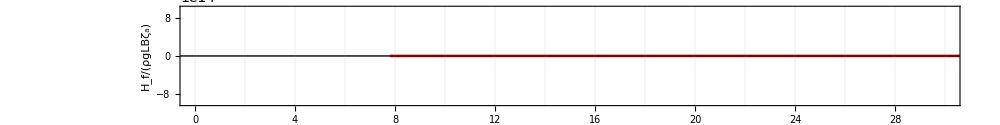

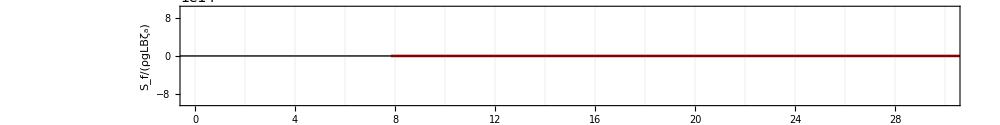

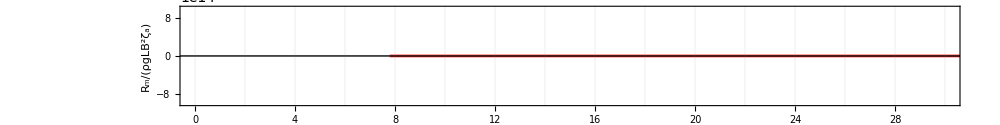

ListPlot::lpn: {{},{{0.,0.0126615},{0.0502001,0.00183025},{0.1004,0.0023423},{0.1506,0.00775449},{0.200801,0.00298018},{0.251001,0.00613242},{0.301201,0.0109158},{0.351401,0.0100242},{0.401601,0.00387457},{0.451801,0.0106189},«252»}}は数値のリストあるいは数値の対のリストではありません．

ListPlot[{{},{{0.,0.0126615},{0.0502001,0.00183025},{0.1004,0.0023423},{0.1506,0.00775449},{0.200801,0.00298018},{0.251001,0.00613242},{0.301201,0.0109158},{0.351401,0.0100242},{0.401601,0.00387457},{0.451801,0.0106189},{0.502001,0.00801694},{0.552202,0.00691184},{0.602402,0.0131494},{0.652602,0.0158759},{0.702802,0.0104053},{0.753002,0.0176497},{0.803202,0.0150446},{0.853402,0.0173972},{0.903603,0.030605},{0.953803,0.0487533},{1.004,0.213162},{1.0542,0.0221017},{1.1044,0.016733},{1.1546,0.0104887},{1.2048,0.00790696},{1.255,0.00983967},{1.3052,0.00895408},{1.3554,0.00837115},{1.4056,0.0105876},{1.4558,0.0129797},{1.506,0.0110208},{1.5562,0.00852263},{1.6064,0.00677192},{1.6566,0.00196376},{1.7068,0.00424611},{1.75701,0.00713805},{1.80721,0.00618219},{1.85741,0.00395604},{1.90761,0.00724936},{1.95781,0.0105814},{2.00801,0.0334456},{2.05821,0.0047654},{2.10841,0.0109796},{2.15861,0.00602826},{2.20881,0.00590655},{2.25901,0.00607736},{2.30921,0.00177069},{2.35941,0.00241249},{2.40961,0.00813904},{2.45981,0.00484024},{2.51001,0.00529671},{2.56021,0.00475433},{2.61041,0.00619329},{2.66061,0.00372342},{2.71081,0.00681956},{2.76101,0.00575537},{2.81121,0.00376179},{2.86141,0.00566329},{2.91161,0.00884346},{2.96181,0.00699705},{3.01201,0.00666731},{3.06221,0.00477765},{3.11241,0.0016242},{3.16261,0.0057534},{3.21281,0.00649305},{3.26301,0.00581887},{3.31321,0.0046138},{3.36341,0.00545435},{3.41361,0.00623159},{3.46381,0.00299173},{3.51401,0.00905898},{3.56421,0.00601456},{3.61441,0.00211755},{3.66461,0.00589666},{3.71481,0.0023159},{3.76501,0.00532677},{3.81521,0.00763731},{3.86541,0.00728319},{3.91561,0.00192144},{3.96581,0.00515179},{4.01601,0.00282233},{4.06621,0.00170203},{4.11641,0.00265439},{4.16661,0.000823804},{4.21681,0.00369994},{4.26701,0.00242641},{4.31721,0.00775429},{4.36741,0.00629635},{4.41761,0.00258675},{4.46781,0.00296377},{4.51801,0.00546017},{4.56821,0.00150021},{4.61841,0.00637646},{4.66861,0.0104609},{4.71881,0.00277005},{4.76901,0.00472958},{4.81921,0.00383671},{4.86941,0.00371585},{4.91961,0.00299744},{4.96981,0.00116667},{5.02001,0.00582479},{5.07021,0.00434139},{5.12041,0.00365702},{5.17062,0.00124893},{5.22082,0.00283528},{5.27102,0.00218221},{5.32122,0.0056182},{5.37142,0.00364633},{5.42162,0.00419323},{5.47182,0.00526149},{5.52202,0.00341667},{5.57222,0.00600744},{5.62242,0.00308155},{5.67262,0.00206991},{5.72282,0.00590215},{5.77302,0.00312457},{5.82322,0.00390261},{5.87342,0.00222576},{5.92362,0.00303447},{5.97382,0.00274452},{6.02402,0.000650857},{6.07422,0.00179229},{6.12442,0.00593121},{6.17462,0.00253613},{6.22482,0.00261612},{6.27502,0.00234897},{6.32522,0.00525342},{6.37542,0.00150041},{6.42562,0.00558306},{6.47582,0.00300851},{6.52602,0.00127514},{6.57622,0.00576422},{6.62642,0.00280912},{6.67662,0.00373725},{6.72682,0.00506043},{6.77702,0.00224112},{6.82722,0.00487348},{6.87742,0.00394453},{6.92762,0.00294849},{6.97782,0.00318041},{7.02802,0.00429912},{7.07822,0.00105656},{7.12842,0.00106756},{7.17862,0.00505105},{7.22882,0.00382786},{7.27902,0.00323962},{7.32922,0.0018992},{7.37942,0.00330621},{7.42962,0.00426078},{7.47982,0.00253969},{7.53002,0.00285069},{7.58022,0.0025481},{7.63042,0.000875554},{7.68062,0.00479512},{7.73082,0.00348627},{7.78102,0.00328709},{7.83122,0.00488145},{7.88142,0.003552},{7.93162,0.00264782},{7.98182,0.00613637},{8.03202,0.00657925},{8.08222,0.00429316},{8.13242,0.00466929},{8.18262,0.00334489},{8.23282,0.00181929},{8.28302,0.00191901},{8.33322,0.00323659},{8.38342,0.00578702},{8.43362,0.00249402},{8.48382,0.00499888},{8.53402,0.00182511},{8.58423,0.00425641},{8.63443,0.00306389},{8.68463,0.00387317},{8.73483,0.00308936},{8.78503,0.00289165},{8.83523,0.00682333},{8.88543,0.00106735},{8.93563,0.00514792},{8.98583,0.00566294},{9.03603,0.00343603},{9.08623,0.00407463},{9.13643,0.00452242},{9.18663,0.00261769},{9.23683,0.00164108},{9.28703,0.00322777},{9.33723,0.00261134},{9.38743,0.00176101},{9.43763,0.00480596},{9.48783,0.00333534},{9.53803,0.00288797},{9.58823,0.000232516},{9.63843,0.00547175},{9.68863,0.000238775},{9.73883,0.0040418},{9.78903,0.00240102},{9.83923,0.00752816},{9.88943,0.00300107},{9.93963,0.00439113},{9.98983,0.00709106},{10.04,0.00225673},{10.0902,0.00392953},{10.1404,0.0032067},{10.1906,0.00314158},{10.2408,0.00325698},{10.291,0.00427736},{10.3412,0.00463341},{10.3914,0.000975135},{10.4416,0.00320483},{10.4918,0.0035808},{10.542,0.00310295},{10.5922,0.00523968},{10.6424,0.00537586},{10.6926,0.00359019},{10.7428,0.00592262},{10.793,0.00247807},{10.8432,0.00534286},{10.8934,0.00510041},{10.9436,0.00169576},{10.9938,0.00648904},{11.044,0.00526392},{11.0942,0.00436896},{11.1444,0.00673466},{11.1946,0.00558875},{11.2448,0.00335472},{11.295,0.00434498},{11.3452,0.00585462},{11.3954,0.000683323},{11.4456,0.006453},{11.4958,0.00349449},{11.546,0.00691067},{11.5962,0.00429143},{11.6464,0.00602401},{11.6966,0.00385744},{11.7468,0.00529073},{11.797,0.00209132},{11.8472,0.0028427},{11.8974,0.00448694},{11.9476,0.00410756},{11.9978,0.00541596},{12.048,0.00434799},{12.0982,0.00596078},{12.1484,0.004515},{12.1986,0.00683936},{12.2488,0.0028382},{12.299,0.00600915},{12.3492,0.00417554},{12.3994,0.00119447},{12.4496,0.00504577},{12.4998,0.0062987},{12.55,0.00455686},{12.6002,0.0023994},{12.6504,0.00678878},{12.7006,0.00150539},{12.7508,0.00229954},{12.801,0.00522544},{12.8512,0.00699333},{12.9014,0.000968162},{12.9516,0.00487832},{13.0018,0.00659088},{13.052,0.00300647},{13.1022,0.00546427}}},PlotRange→{{0,3},All},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

ListPlot::lpn: {{},{{0.,0.0239023},{0.0501233,0.0150011},{0.100247,0.00431079},{0.15037,0.0042859},{0.200493,0.00773119},{0.250617,0.00108427},{0.30074,0.00353431},{0.350863,0.00819787},{0.400987,0.00563792},{0.45111,0.0079937},«302»}}は数値のリストあるいは数値の対のリストではありません．

ListPlot[{{},{{0.,0.0239023},{0.0501233,0.0150011},{0.100247,0.00431079},{0.15037,0.0042859},{0.200493,0.00773119},{0.250617,0.00108427},{0.30074,0.00353431},{0.350863,0.00819787},{0.400987,0.00563792},{0.45111,0.0079937},{0.501233,0.0144043},{0.551357,0.00681485},{0.60148,0.00597083},{0.651603,0.00828855},{0.701727,0.00807829},{0.75185,0.0113535},{0.801973,0.0116307},{0.852097,0.0213771},{0.90222,0.0423303},{0.952343,0.0605972},{1.00247,0.259458},{1.05259,0.0197451},{1.10271,0.0255598},{1.15284,0.0228639},{1.20296,0.00709876},{1.25308,0.00942459},{1.30321,0.0101802},{1.35333,0.00442917},{1.40345,0.00240436},{1.45358,0.00501745},{1.5037,0.00940595},{1.55382,0.00690102},{1.60395,0.00459262},{1.65407,0.00812946},{1.70419,0.0069858},{1.75432,0.00341624},{1.80444,0.00475375},{1.85456,0.00417703},{1.90469,0.00518797},{1.95481,0.00333349},{2.00493,0.0164455},{2.05506,0.00667047},{2.10518,0.00432011},{2.1553,0.00648326},{2.20543,0.00115951},{2.25555,0.00510485},{2.30567,0.00479131},{2.3558,0.00492647},{2.40592,0.000714826},{2.45604,0.00366142},{2.50617,0.00860847},{2.55629,0.00374938},{2.60641,0.00212306},{2.65654,0.00516246},{2.70666,0.00245961},{2.75678,0.00330214},{2.80691,0.00213398},{2.85703,0.00239686},{2.90715,0.00641563},{2.95728,0.00128451},{3.0074,0.00615572},{3.05752,0.00511089},{3.10765,0.00227862},{3.15777,0.00700964},{3.20789,0.00416889},{3.25802,0.00205297},{3.30814,0.0058544},{3.35826,0.00472743},{3.40839,0.00323831},{3.45851,0.00304172},{3.50863,0.0046623},{3.55876,0.00328238},{3.60888,0.00108314},{3.659,0.00507334},{3.70913,0.0029104},{3.75925,0.00517153},{3.80937,0.0012714},{3.8595,0.00201616},{3.90962,0.00539452},{3.95974,0.00121345},{4.00987,0.00094456},{4.05999,0.00536154},{4.11011,0.00426496},{4.16024,0.00372371},{4.21036,0.00508306},{4.26048,0.00333509},{4.31061,0.00914114},{4.36073,0.00499988},{4.41085,0.00217375},{4.46098,0.00341954},{4.5111,0.00606417},{4.56122,0.00313461},{4.61135,0.00179557},{4.66147,0.00355242},{4.71159,0.00096332},{4.76172,0.00457123},{4.81184,0.00304592},{4.86196,0.000580919},{4.91209,0.00652073},{4.96221,0.00187598},{5.01233,0.00324683},{5.06246,0.00400675},{5.11258,0.00217166},{5.1627,0.00375868},{5.21283,0.000381447},{5.26295,0.00138093},{5.31307,0.00630435},{5.3632,0.0036321},{5.41332,0.00215722},{5.46344,0.00249939},{5.51357,0.00486846},{5.56369,0.00300565},{5.61381,0.00279668},{5.66394,0.00348749},{5.71406,0.00260066},{5.76418,0.00686571},{5.81431,0.00321175},{5.86443,0.00255138},{5.91455,0.0053439},{5.96468,0.00203972},{6.0148,0.00168343},{6.06492,0.00386796},{6.11505,0.00237407},{6.16517,0.00435987},{6.21529,0.00148198},{6.26542,0.00277168},{6.31554,0.00423363},{6.36566,0.00338968},{6.41579,0.00265366},{6.46591,0.00510175},{6.51603,0.00310806},{6.56616,0.00363695},{6.61628,0.00117308},{6.6664,0.00374225},{6.71653,0.00301922},{6.76665,0.00374828},{6.81677,0.00141372},{6.8669,0.00150084},{6.91702,0.00432351},{6.96714,0.00113331},{7.01727,0.00298231},{7.06739,0.00178596},{7.11751,0.00168385},{7.16764,0.00292559},{7.21776,0.000993477},{7.26788,0.00261464},{7.31801,0.00534314},{7.36813,0.00364713},{7.41825,0.00091723},{7.46838,0.00244497},{7.5185,0.00244863},{7.56862,0.00371195},{7.61875,0.00147453},{7.66887,0.00104283},{7.71899,0.00346836},{7.76912,0.00518053},{7.81924,0.0023503},{7.86936,0.000988162},{7.91949,0.00177859},{7.96961,0.00251598},{8.01973,0.00360092},{8.06986,0.00308853},{8.11998,0.00214005},{8.1701,0.00310262},{8.22023,0.00100697},{8.27035,0.000296733},{8.32047,0.0037627},{8.3706,0.00163447},{8.42072,0.00315425},{8.47084,0.00381739},{8.52097,0.00132685},{8.57109,0.00175025},{8.62121,0.000702708},{8.67134,0.00114954},{8.72146,0.00325029},{8.77158,0.00153327},{8.82171,0.00282352},{8.87183,0.00205744},{8.92195,0.00216523},{8.97208,0.00202444},{9.0222,0.00138161},{9.07232,0.00139139},{9.12245,0.00224445},{9.17257,0.00436516},{9.22269,0.00172849},{9.27282,0.00172615},{9.32294,0.00294478},{9.37306,0.00098614},{9.42319,0.00190853},{9.47331,0.00335625},{9.52343,0.00342522},{9.57356,0.00225712},{9.62368,0.00145017},{9.6738,0.00144498},{9.72393,0.00309866},{9.77405,0.0014188},{9.82417,0.000495129},{9.8743,0.00265714},{9.92442,0.00260909},{9.97454,0.0038279},{10.0247,0.00263232},{10.0748,0.000812626},{10.1249,0.00313165},{10.175,0.0021104},{10.2252,0.00133959},{10.2753,0.00121572},{10.3254,0.00420632},{10.3755,0.00284931},{10.4257,0.00142952},{10.4758,0.000700998},{10.5259,0.000964202},{10.576,0.00237369},{10.6261,0.00070342},{10.6763,0.00104408},{10.7264,0.00239228},{10.7765,0.000490131},{10.8266,0.00158933},{10.8768,0.00264718},{10.9269,0.000423504},{10.977,0.00338129},{11.0271,0.00149817},{11.0773,0.000840608},{11.1274,0.00225192},{11.1775,0.00239985},{11.2276,0.00123057},{11.2777,0.00244592},{11.3279,0.00222682},{11.378,0.00121863},{11.4281,0.000838299},{11.4782,0.00267847},{11.5284,0.00219948},{11.5785,0.0026574},{11.6286,0.00140222},{11.6787,0.00149276},{11.7289,0.00274399},{11.779,0.000688759},{11.8291,0.000752141},{11.8792,0.00138106},{11.9294,0.000375359},{11.9795,0.00174772},{12.0296,0.0017413},{12.0797,0.00130774},{12.1298,0.00342709},{12.18,0.00338935},{12.2301,0.00111607},{12.2802,0.00200301},{12.3303,0.00274858},{12.3805,0.000962843},{12.4306,0.00181968},{12.4807,0.00192556},{12.5308,0.00115246},{12.581,0.00119564},{12.6311,0.00197082},{12.6812,0.000442348},{12.7313,0.00145455},{12.7814,0.0011502},{12.8316,0.000998299},{12.8817,0.00129252},{12.9318,0.00164747},{12.9819,0.00149602},{13.0321,0.0033283},{13.0822,0.000727964},{13.1323,0.00182448},{13.1824,0.00163422},{13.2326,0.00137876},{13.2827,0.00241317},{13.3328,0.00139648},{13.3829,0.00130712},{13.4331,0.000065565},{13.4832,0.000990201},{13.5333,0.000639866},{13.5834,0.00067349},{13.6335,0.00166566},{13.6837,0.00205242},{13.7338,0.00150027},{13.7839,0.00100646},{13.834,0.00110755},{13.8842,0.000865622},{13.9343,0.00148583},{13.9844,0.000927881},{14.0345,0.00133334},{14.0847,0.0015259},{14.1348,0.00112952},{14.1849,0.00103184},{14.235,0.000238637},{14.2851,0.000845999},{14.3353,0.00106042},{14.3854,0.00151325},{14.4355,0.000255428},{14.4856,0.00088411},{14.5358,0.000700666},{14.5859,0.00130072},{14.636,0.000790048},{14.6861,0.00132622},{14.7363,0.000544464},{14.7864,0.000196936},{14.8365,0.000947775},{14.8866,0.00248037},{14.9368,0.000955668},{14.9869,0.00310144},{15.037,0.00406226},{15.0871,0.000547995},{15.1372,0.000747303},{15.1874,0.000540295},{15.2375,0.0022732},{15.2876,0.00152876},{15.3377,0.00167998},{15.3879,0.000819488},{15.438,0.000317396},{15.4881,0.00226509},{15.5382,0.00150412},{15.5884,0.000811698}}},PlotRange→{{0,3},All},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

ListPlot::lpn: {{},{{0.,0.000640236},{0.0500558,0.0000781921},{0.100112,0.00026843},{0.150168,0.000339601},{0.200223,0.00010371},{0.250279,0.000219389},{0.300335,0.000192647},{0.350391,0.000102889},{0.400447,0.00017189},{0.450503,0.000205041},«278»}}は数値のリストあるいは数値の対のリストではありません．

ListPlot[{{},{{0.,0.000640236},{0.0500558,0.0000781921},{0.100112,0.00026843},{0.150168,0.000339601},{0.200223,0.00010371},{0.250279,0.000219389},{0.300335,0.000192647},{0.350391,0.000102889},{0.400447,0.00017189},{0.450503,0.000205041},{0.500558,0.000207725},{0.550614,0.000119294},{0.60067,0.000161854},{0.650726,0.0000841088},{0.700782,0.000239592},{0.750838,0.000280093},{0.800893,0.000123902},{0.850949,0.000667865},{0.901005,0.000962687},{0.951061,0.000668998},{1.00112,0.00549722},{1.05117,0.0012618},{1.10123,0.000405379},{1.15128,0.000316587},{1.20134,0.000168337},{1.2514,0.000154743},{1.30145,0.0000814285},{1.35151,0.0000318426},{1.40156,0.000204424},{1.45162,0.000159464},{1.50168,0.0000283558},{1.55173,0.000140198},{1.60179,0.000156441},{1.65184,0.000100844},{1.7019,0.000171752},{1.75195,0.000145378},{1.80201,0.000116035},{1.85207,0.000172482},{1.90212,0.000449095},{1.95218,0.000375715},{2.00223,0.00158011},{2.05229,0.000366696},{2.10235,0.000456588},{2.1524,0.000383655},{2.20246,0.000129591},{2.25251,0.000202778},{2.30257,0.000122728},{2.35262,0.0000721879},{2.40268,0.000328709},{2.45274,0.000086229},{2.50279,0.000122962},{2.55285,0.0000744263},{2.6029,0.000191156},{2.65296,0.000212494},{2.70302,0.000132869},{2.75307,0.000120984},{2.80313,0.0000579548},{2.85318,0.000206059},{2.90324,0.000038342},{2.95329,0.000153558},{3.00335,0.000183636},{3.05341,0.000118667},{3.10346,0.000136303},{3.15352,0.0000708915},{3.20357,0.000129648},{3.25363,0.0000116752},{3.30369,0.000165252},{3.35374,0.0000171454},{3.4038,0.000221004},{3.45385,0.0000820458},{3.50391,0.0000408945},{3.55396,0.0000910554},{3.60402,0.0000851604},{3.65408,0.0000254674},{3.70413,0.000030326},{3.75419,0.000130977},{3.80424,0.0000472182},{3.8543,0.000156344},{3.90436,0.00019478},{3.95441,0.0000677},{4.00447,0.000256821},{4.05452,0.000117234},{4.10458,0.0000825967},{4.15463,0.000116437},{4.20469,0.000167403},{4.25475,0.00021899},{4.3048,0.0000495195},{4.35486,0.0000342137},{4.40491,0.0000831524},{4.45497,0.000142255},{4.50503,0.000200126},{4.55508,0.0000773855},{4.60514,0.0000680847},{4.65519,0.000165176},{4.70525,0.000188115},{4.7553,0.000157351},{4.80536,0.000111475},{4.85542,0.000137251},{4.90547,0.000121758},{4.95553,0.000177959},{5.00558,0.000120088},{5.05564,0.00013163},{5.1057,0.000139099},{5.15575,0.00013088},{5.20581,0.000249375},{5.25586,0.000205811},{5.30592,0.0000917974},{5.35597,0.000125982},{5.40603,0.000090696},{5.45609,0.000169533},{5.50614,0.000153639},{5.5562,0.0000432355},{5.60625,0.0000394229},{5.65631,0.000179635},{5.70637,0.00015488},{5.75642,0.0000365764},{5.80648,4.10435×10^-6},{5.85653,0.0000764669},{5.90659,0.000178285},{5.95664,0.000130788},{6.0067,0.0000975529},{6.05676,0.0000607639},{6.10681,0.000112897},{6.15687,0.0000950328},{6.20692,0.0000677339},{6.25698,0.0001148},{6.30704,0.0000554231},{6.35709,0.000143513},{6.40715,0.000179788},{6.4572,0.000183074},{6.50726,0.000101576},{6.55731,0.000128946},{6.60737,0.000157237},{6.65743,0.000219506},{6.70748,0.0000756265},{6.75754,0.000106149},{6.80759,0.000106948},{6.85765,0.000147112},{6.90771,0.0000426554},{6.95776,0.0000603732},{7.00782,0.000090655},{7.05787,0.000060404},{7.10793,0.00014865},{7.15798,0.0000892526},{7.20804,0.0000867416},{7.2581,0.000144703},{7.30815,0.000086257},{7.35821,0.000117664},{7.40826,0.000113697},{7.45832,0.000121224},{7.50838,0.00010177},{7.55843,0.0000987211},{7.60849,0.000104859},{7.65854,0.000173906},{7.7086,0.00010961},{7.75865,0.000100355},{7.80871,0.000127098},{7.85877,0.000156849},{7.90882,0.000132844},{7.95888,0.000085912},{8.00893,0.000119034},{8.05899,0.000165703},{8.10905,0.0000651868},{8.1591,0.0000730732},{8.20916,0.000110839},{8.25921,0.000118993},{8.30927,0.0000830297},{8.35932,0.0000762546},{8.40938,0.0000813793},{8.45944,0.0000594631},{8.50949,0.000223538},{8.55955,0.0000626666},{8.6096,0.000119468},{8.65966,0.00016102},{8.70972,0.0000934476},{8.75977,0.0000716342},{8.80983,0.000124576},{8.85988,0.000179757},{8.90994,0.00011112},{8.95999,0.0000690411},{9.01005,0.0000720407},{9.06011,0.000209402},{9.11016,0.000112795},{9.16022,0.000113459},{9.21027,0.0000487533},{9.26033,0.0000965651},{9.31039,0.000130005},{9.36044,0.000152547},{9.4105,0.0000623233},{9.46055,0.000120451},{9.51061,0.00026041},{9.56066,0.0000799653},{9.61072,0.000193895},{9.66078,0.0000448459},{9.71083,0.0000801249},{9.76089,0.0000584693},{9.81094,0.000164606},{9.861,0.000121617},{9.91106,0.0000785443},{9.96111,0.0000281966},{10.0112,0.0000977613},{10.0612,0.000251432},{10.1113,0.000102294},{10.1613,0.0000996791},{10.2114,0.0000287285},{10.2614,0.000210228},{10.3115,0.000182416},{10.3616,0.000128525},{10.4116,0.0000418784},{10.4617,0.0000992152},{10.5117,0.000170317},{10.5618,0.0000421288},{10.6118,0.000144882},{10.6619,0.0000271239},{10.7119,0.000130449},{10.762,0.0000474782},{10.8121,0.000141851},{10.8621,0.0000547773},{10.9122,0.0000889572},{10.9622,0.00005435},{11.0123,0.000101668},{11.0623,0.00013022},{11.1124,0.0000509022},{11.1625,0.0000616216},{11.2125,0.000111453},{11.2626,0.00014541},{11.3126,0.0000568986},{11.3627,0.0000587593},{11.4127,0.0000229568},{11.4628,0.0000648389},{11.5128,0.000137752},{11.5629,0.0000375627},{11.613,0.000114869},{11.663,0.0000635141},{11.7131,0.000128498},{11.7631,0.0000595724},{11.8132,0.0000833699},{11.8632,0.0000460903},{11.9133,0.000145946},{11.9633,0.0000620988},{12.0134,0.000116091},{12.0635,0.0000741995},{12.1135,0.000099779},{12.1636,0.0000474538},{12.2136,0.000148429},{12.2637,0.000108366},{12.3137,0.0000646994},{12.3638,0.0000504644},{12.4138,0.0000406527},{12.4639,0.000052094},{12.514,0.0000554473},{12.564,0.0000373781},{12.6141,0.0000760887},{12.6641,0.000118414},{12.7142,0.000087496},{12.7642,0.0000306856},{12.8143,0.0000286541},{12.8643,0.0000615592},{12.9144,0.000119674},{12.9645,0.0000541565},{13.0145,0.000099514},{13.0646,0.0000364598},{13.1146,0.000110045},{13.1647,0.0000752239},{13.2147,0.000159825},{13.2648,0.0000455832},{13.3149,0.000117317},{13.3649,0.0000611533},{13.415,0.0000927636},{13.465,0.0000405644},{13.5151,0.000073428},{13.5651,0.0000956829},{13.6152,0.000111524},{13.6652,0.0000755464},{13.7153,0.000038194},{13.7654,0.0000338958},{13.8154,0.0000407935},{13.8655,0.0000447351},{13.9155,0.0000232118},{13.9656,0.0000413239},{14.0156,0.0000859849},{14.0657,9.63471×10^-6},{14.1157,0.000131066},{14.1658,0.0000196786},{14.2159,0.000115102},{14.2659,0.0000976702},{14.316,0.000114906},{14.366,0.000051613}}},Epilog→Line[{{0.561798,0},{0.561798,10}}],PlotRange→{{0,3},All},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

```mathematica
ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,((importData[json,"float_force",i]-importData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,3,3,1}],
SimuHf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,((importData[json,"float_force",i]-importData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,1,1,1}],
SimuSf],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["S_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{importData[json,"simulation_time"]/Tw,-((importData[json,"float_torque",i]-importData[json,"float_torque",i][[15]])/(ρ*g*L*B*B*ζa))}ᵀ,{i,2,2,1}],
SimuRm],
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["R_m/(ρgLB^2ζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]


ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,((importData[json,"float_force",3]-importData[json,"float_force",3][[5]])/(ρ*g*L*B*ζa)),{10,30}],
interpolateAndFourierTr[SimuHf,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,((importData[json,"float_force",1]-importData[json,"float_force",1][[5]])/(ρ*g*L*B*ζa)),{10,30}],
interpolateAndFourierTr[SimuSf,{10,30}]
},
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,-((importData[json,"float_torque",2]-importData[json,"float_torque",2][[15]])/(ρ*g*L*B*B*ζa)),{15,30}],
interpolateAndFourierTr[SimuRm,{10,30}]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
Evaluate[plot2Doption]
]
```

浮体が流体から受ける，鉛直水平方向の力，y軸回転方向のトルクは，Tanizawa1997の結果とよく一致している．

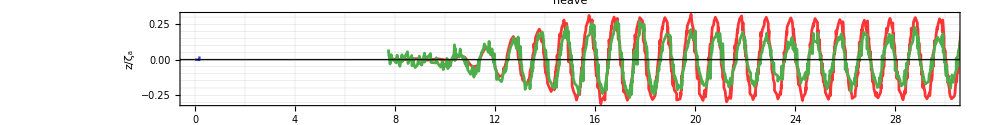

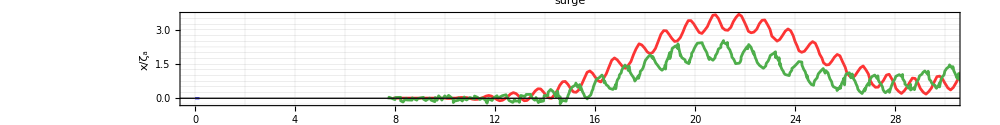

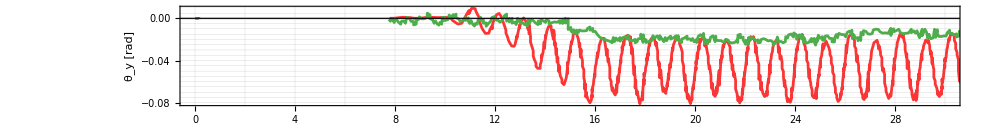

ListPlot::lpn: {{},{{0.,0.0526283},{0.0505737,0.012794},{0.101147,0.0319098},{0.151721,0.00730915},{0.202295,0.0329488},{0.252869,0.0310894},{0.303442,0.0194287},{0.354016,0.022282},{0.40459,0.0209483},{0.455163,0.0365695},«249»}}は数値のリストあるいは数値の対のリストではありません．

ListPlot[{{},{{0.,0.0526283},{0.0505737,0.012794},{0.101147,0.0319098},{0.151721,0.00730915},{0.202295,0.0329488},{0.252869,0.0310894},{0.303442,0.0194287},{0.354016,0.022282},{0.40459,0.0209483},{0.455163,0.0365695},{0.505737,0.00316335},{0.556311,0.0439938},{0.606885,0.013335},{0.657458,0.0252435},{0.708032,0.0233935},{0.758606,0.0279889},{0.809179,0.041865},{0.859753,0.0353365},{0.910327,0.0512816},{0.960901,0.123855},{1.01147,0.265041},{1.06205,0.0235816},{1.11262,0.0317596},{1.1632,0.00592051},{1.21377,0.0196425},{1.26434,0.0263868},{1.31492,0.00636832},{1.36549,0.0319938},{1.41606,0.0223896},{1.46664,0.0250725},{1.51721,0.0121641},{1.56779,0.0382386},{1.61836,0.0144003},{1.66893,0.0203465},{1.71951,0.00633104},{1.77008,0.00613163},{1.82065,0.041664},{1.87123,0.0185754},{1.9218,0.0305502},{1.97237,0.0226626},{2.02295,0.0344565},{2.07352,0.00902613},{2.1241,0.0343626},{2.17467,0.022171},{2.22524,0.00889167},{2.27582,0.0210405},{2.32639,0.010923},{2.37696,0.0353011},{2.42754,0.0251771},{2.47811,0.0181042},{2.52869,0.0122645},{2.57926,0.0246757},{2.62983,0.0175068},{2.68041,0.00994362},{2.73098,0.01323},{2.78155,0.00679581},{2.83213,0.0339303},{2.8827,0.0171653},{2.93328,0.0223352},{2.98385,0.0273868},{3.03442,0.0227983},{3.085,0.0184951},{3.13557,0.0164617},{3.18614,0.0203793},{3.23672,0.0128157},{3.28729,0.0170283},{3.33786,0.0103835},{3.38844,0.0287117},{3.43901,0.0224458},{3.48959,0.0149829},{3.54016,0.0236204},{3.59073,0.0120933},{3.64131,0.0122867},{3.69188,0.00760578},{3.74245,0.0200702},{3.79303,0.0204069},{3.8436,0.0196522},{3.89418,0.0146148},{3.94475,0.0274315},{3.99532,0.0289456},{4.0459,0.0118476},{4.09647,0.0165654},{4.14704,0.0169716},{4.19762,0.022381},{4.24819,0.0227073},{4.29877,0.0110147},{4.34934,0.0147178},{4.39991,0.0199634},{4.45049,0.0209984},{4.50106,0.0134805},{4.55163,0.0175214},{4.60221,0.0163692},{4.65278,0.0115573},{4.70336,0.00489072},{4.75393,0.0211325},{4.8045,0.0179494},{4.85508,0.0107568},{4.90565,0.0126637},{4.95622,0.0157561},{5.0068,0.0190704},{5.05737,0.014229},{5.10794,0.0132871},{5.15852,0.00799056},{5.20909,0.00882705},{5.25967,0.0202789},{5.31024,0.00688651},{5.36081,0.0193654},{5.41139,0.0137372},{5.46196,0.0149803},{5.51253,0.0154933},{5.56311,0.0244766},{5.61368,0.00503283},{5.66426,0.0100307},{5.71483,0.00632693},{5.7654,0.0114122},{5.81598,0.0240999},{5.86655,0.00648395},{5.91712,0.0209676},{5.9677,0.0205804},{6.01827,0.0229983},{6.06885,0.0124443},{6.11942,0.0214906},{6.16999,0.0108937},{6.22057,0.00151191},{6.27114,0.0157555},{6.32171,0.00803032},{6.37229,0.0294267},{6.42286,0.0142768},{6.47343,0.0201145},{6.52401,0.0178279},{6.57458,0.0275172},{6.62516,0.00677823},{6.67573,0.0125778},{6.7263,0.00600959},{6.77688,0.010082},{6.82745,0.0235792},{6.87802,0.0111956},{6.9286,0.0159227},{6.97917,0.0158379},{7.02975,0.0213733},{7.08032,0.0111837},{7.13089,0.0148892},{7.18147,0.00348799},{7.23204,0.00696389},{7.28261,0.0147252},{7.33319,0.00555388},{7.38376,0.0248776},{7.43434,0.0102707},{7.48491,0.0225359},{7.53548,0.0133839},{7.58606,0.0164506},{7.63663,0.00271232},{7.6872,0.0150174},{7.73778,0.0136255},{7.78835,0.00487609},{7.83893,0.017749},{7.8895,0.0135108},{7.94007,0.0226264},{7.99065,0.00962599},{8.04122,0.0133701},{8.09179,0.0109347},{8.14237,0.00912027},{8.19294,0.0147489},{8.24351,0.0135738},{8.29409,0.0157876},{8.34466,0.0124781},{8.39524,0.0301984},{8.44581,0.00746859},{8.49638,0.0213488},{8.54696,0.01407},{8.59753,0.0130128},{8.6481,0.00224888},{8.69868,0.00560851},{8.74925,0.0122218},{8.79983,0.010919},{8.8504,0.0137672},{8.90097,0.00691192},{8.95155,0.0168833},{9.00212,0.00292864},{9.05269,0.0122599},{9.10327,0.00693672},{9.15384,0.000529322},{9.20442,0.0129531},{9.25499,0.013602},{9.30556,0.0187857},{9.35614,0.00956152},{9.40671,0.0231355},{9.45728,0.0102245},{9.50786,0.0179432},{9.55843,0.00633639},{9.60901,0.00792169},{9.65958,0.00276043},{9.71015,0.00283372},{9.76073,0.017449},{9.8113,0.00922448},{9.86187,0.00917737},{9.91245,0.0108051},{9.96302,0.0106198},{10.0136,0.00265738},{10.0642,0.010603},{10.1147,0.00634971},{10.1653,0.00983299},{10.2159,0.0119883},{10.2665,0.0116197},{10.317,0.0166229},{10.3676,0.0141171},{10.4182,0.0135716},{10.4688,0.00781574},{10.5193,0.0133218},{10.5699,0.0087161},{10.6205,0.00463611},{10.6711,0.00240022},{10.7216,0.00181881},{10.7722,0.0122446},{10.8228,0.00928889},{10.8733,0.0125069},{10.9239,0.0091861},{10.9745,0.00595308},{11.0251,0.00357217},{11.0756,0.00386359},{11.1262,0.00371041},{11.1768,0.0101503},{11.2274,0.0103855},{11.2779,0.0132932},{11.3285,0.0122325},{11.3791,0.0103567},{11.4297,0.00908084},{11.4802,0.00654751},{11.5308,0.00761525},{11.5814,0.00599056},{11.632,0.00370404},{11.6825,0.00183591},{11.7331,0.00685655},{11.7837,0.00366832},{11.8342,0.00704241},{11.8848,0.00686306},{11.9354,0.00671064},{11.986,0.0051806},{12.0365,0.0052361},{12.0871,0.00124357},{12.1377,0.00707498},{12.1883,0.00928932},{12.2388,0.00672646},{12.2894,0.0111126},{12.34,0.012789},{12.3906,0.00934734},{12.4411,0.00346503},{12.4917,0.00336092},{12.5423,0.00426326},{12.5929,0.00588613},{12.6434,0.00362464},{12.694,0.00370432},{12.7446,0.0051959},{12.7951,0.00616674},{12.8457,0.00928069},{12.8963,0.00341373},{12.9469,0.00718411},{12.9974,0.0065121},{13.048,0.00842507}}},PlotRange→{{0,3},All},PlotLegends→{present simulation,Tanizawa},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

ListPlot::lpn: {{},{{0.,2.91029},{0.0502635,1.62261},{0.100527,0.27258},{0.15079,0.0374569},{0.201054,0.0472464},{0.251317,0.0390198},{0.301581,0.0343567},{0.351844,0.0285308},{0.402108,0.0253292},{0.452371,0.0242775},«84»}}は数値のリストあるいは数値の対のリストではありません．

ListPlot[{{},{{0.,2.91029},{0.0502635,1.62261},{0.100527,0.27258},{0.15079,0.0374569},{0.201054,0.0472464},{0.251317,0.0390198},{0.301581,0.0343567},{0.351844,0.0285308},{0.402108,0.0253292},{0.452371,0.0242775},{0.502635,0.0199136},{0.552898,0.020803},{0.603162,0.019071},{0.653425,0.0197488},{0.703689,0.0172284},{0.753952,0.0139291},{0.804216,0.021053},{0.854479,0.0270015},{0.904743,0.0392346},{0.955006,0.0308357},{1.00527,0.321737},{1.05553,0.0567017},{1.1058,0.0242161},{1.15606,0.0239861},{1.20632,0.0162419},{1.25659,0.0153807},{1.30685,0.0132411},{1.35711,0.0149515},{1.40738,0.00983469},{1.45764,0.0113696},{1.5079,0.0101919},{1.55817,0.00990623},{1.60843,0.00935129},{1.65869,0.00841144},{1.70896,0.0100965},{1.75922,0.00638581},{1.80949,0.00708185},{1.85975,0.00808965},{1.91001,0.0118836},{1.96028,0.0060525},{2.01054,0.0214587},{2.0608,0.00632491},{2.11107,0.00390412},{2.16133,0.00656463},{2.21159,0.00461987},{2.26186,0.00530043},{2.31212,0.00414538},{2.36238,0.00593861},{2.41265,0.00640289},{2.46291,0.00523233},{2.51317,0.00387386},{2.56344,0.00547901},{2.6137,0.00357087},{2.66396,0.0060953},{2.71423,0.00398942},{2.76449,0.0084736},{2.81475,0.0050849},{2.86502,0.00384067},{2.91528,0.0056757},{2.96555,0.00347805},{3.01581,0.00234917},{3.06607,0.00693777},{3.11634,0.00295311},{3.1666,0.00486672},{3.21686,0.00413101},{3.26713,0.00427275},{3.31739,0.00487318},{3.36765,0.00605236},{3.41792,0.00273635},{3.46818,0.00354471},{3.51844,0.00206516},{3.56871,0.00545967},{3.61897,0.00639616},{3.66923,0.00291953},{3.7195,0.00533497},{3.76976,0.00641975},{3.82002,0.00671096},{3.87029,0.00144098},{3.92055,0.00315477},{3.97081,0.00291012},{4.02108,0.0044718},{4.07134,0.00957227},{4.12161,0.00499754},{4.17187,0.00447264},{4.22213,0.00565192},{4.2724,0.00262803},{4.32266,0.00567471},{4.37292,0.00599418},{4.42319,0.00375171},{4.47345,0.00450992},{4.52371,0.00262659},{4.57398,0.00226548},{4.62424,0.00650354},{4.6745,0.00548679}}},PlotRange→{{0,3},All},PlotLegends→{present simulation,Tanizawa},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

ListPlot::lpn: {{},{{0.,0.074018},{0.0502352,0.0139338},{0.10047,0.010487},{0.150706,0.00721041},{0.200941,0.004279},{0.251176,0.00303809},{0.301411,0.00270637},{0.351646,0.00244713},{0.401881,0.00154042},{0.452117,0.00190006},«237»}}は数値のリストあるいは数値の対のリストではありません．

ListPlot[{{},{{0.,0.074018},{0.0502352,0.0139338},{0.10047,0.010487},{0.150706,0.00721041},{0.200941,0.004279},{0.251176,0.00303809},{0.301411,0.00270637},{0.351646,0.00244713},{0.401881,0.00154042},{0.452117,0.00190006},{0.502352,0.00380493},{0.552587,0.000711107},{0.602822,0.00131922},{0.653057,0.0013744},{0.703292,0.00150299},{0.753528,0.00100476},{0.803763,0.00168872},{0.853998,0.00291855},{0.904233,0.00502985},{0.954468,0.00454388},{1.0047,0.0248592},{1.05494,0.00415251},{1.10517,0.00148262},{1.15541,0.00102562},{1.20564,0.000998178},{1.25588,0.00112333},{1.30611,0.000929487},{1.35635,0.000638259},{1.40658,0.000676846},{1.45682,0.000719838},{1.50706,0.00110167},{1.55729,0.00068946},{1.60753,0.000616193},{1.65776,0.000335563},{1.708,0.000540359},{1.75823,0.000495469},{1.80847,0.000483725},{1.8587,0.000907409},{1.90894,0.00068657},{1.95917,0.000679304},{2.00941,0.00223206},{2.05964,0.000652295},{2.10988,0.000355278},{2.16011,0.00031747},{2.21035,0.000322191},{2.26058,0.000247839},{2.31082,0.000324051},{2.36105,0.000149784},{2.41129,0.000308652},{2.46152,0.000361877},{2.51176,0.0000968896},{2.56199,0.000251588},{2.61223,0.000482313},{2.66246,0.000341696},{2.7127,0.000426205},{2.76293,0.000366089},{2.81317,0.000486862},{2.86341,0.000494177},{2.91364,0.000389313},{2.96388,0.00052038},{3.01411,0.000161378},{3.06435,0.00019738},{3.11458,0.000336175},{3.16482,0.000185937},{3.21505,0.000361656},{3.26529,0.000372563},{3.31552,0.000175604},{3.36576,0.00041891},{3.41599,0.00028306},{3.46623,0.000256623},{3.51646,0.000249395},{3.5667,0.000328102},{3.61693,0.000287782},{3.66717,0.000160391},{3.7174,0.000544476},{3.76764,0.000591504},{3.81787,0.000152211},{3.86811,0.000147146},{3.91834,0.000629838},{3.96858,0.000510259},{4.01881,0.000333053},{4.06905,0.000489051},{4.11928,0.000188329},{4.16952,0.000497954},{4.21975,0.00019757},{4.26999,0.00040377},{4.32023,0.000278862},{4.37046,0.000374218},{4.4207,0.000317824},{4.47093,0.000325679},{4.52117,0.000222948},{4.5714,0.000172693},{4.62164,0.000434837},{4.67187,0.000296573},{4.72211,0.000169266},{4.77234,0.000250035},{4.82258,0.000548692},{4.87281,0.000222677},{4.92305,0.00022846},{4.97328,0.000291125},{5.02352,0.000236097},{5.07375,0.0000890131},{5.12399,0.000111758},{5.17422,0.000800223},{5.22446,0.000123483},{5.27469,0.00019559},{5.32493,0.000618893},{5.37516,0.000157584},{5.4254,0.000261111},{5.47563,0.000266977},{5.52587,0.000194251},{5.5761,0.000265114},{5.62634,0.000371741},{5.67657,0.00043268},{5.72681,0.000305435},{5.77705,0.000316562},{5.82728,0.000316059},{5.87752,0.000419701},{5.92775,0.000363189},{5.97799,0.000245707},{6.02822,0.00016811},{6.07846,0.000346618},{6.12869,0.000512616},{6.17893,0.000359933},{6.22916,0.00038332},{6.2794,0.00020907},{6.32963,0.0000712199},{6.37987,0.000488774},{6.4301,0.000372045},{6.48034,0.00041545},{6.53057,0.000411357},{6.58081,0.000415611},{6.63104,0.000284951},{6.68128,0.000280174},{6.73151,0.000193268},{6.78175,0.000210581},{6.83198,0.000446555},{6.88222,0.000477137},{6.93245,0.000210907},{6.98269,0.000377171},{7.03292,0.000388252},{7.08316,0.000397307},{7.1334,0.000476748},{7.18363,0.000327754},{7.23387,0.000448574},{7.2841,0.000368891},{7.33434,0.000326572},{7.38457,0.000310355},{7.43481,0.00051538},{7.48504,0.000369265},{7.53528,0.000479816},{7.58551,0.000192045},{7.63575,0.000191233},{7.68598,0.000161796},{7.73622,0.000394424},{7.78645,0.000269756},{7.83669,0.000316063},{7.88692,0.000236613},{7.93716,0.0004085},{7.98739,0.000633283},{8.03763,0.000247997},{8.08786,0.000377042},{8.1381,0.0000811423},{8.18833,0.000284503},{8.23857,0.000083878},{8.2888,0.000407202},{8.33904,0.0000779995},{8.38927,0.000340499},{8.43951,0.00049486},{8.48974,0.0000690158},{8.53998,0.00036307},{8.59022,0.000377767},{8.64045,0.000150422},{8.69069,0.000351384},{8.74092,0.000153144},{8.79116,0.000091843},{8.84139,0.000302349},{8.89163,0.000559869},{8.94186,0.0000423962},{8.9921,0.000351096},{9.04233,0.000474497},{9.09257,0.000259832},{9.1428,0.0000874747},{9.19304,0.000254465},{9.24327,0.000371912},{9.29351,0.000458875},{9.34374,0.000376318},{9.39398,0.00050701},{9.44421,0.000230348},{9.49445,0.00007493},{9.54468,0.000127388},{9.59492,0.00045736},{9.64515,0.0000276327},{9.69539,0.00029784},{9.74562,0.000410165},{9.79586,0.000311094},{9.84609,0.000281891},{9.89633,0.000525119},{9.94657,0.0000538116},{9.9968,0.000148317},{10.047,0.000393663},{10.0973,0.0000706294},{10.1475,0.000376404},{10.1977,0.000374484},{10.248,0.000342075},{10.2982,0.000121102},{10.3484,0.000393744},{10.3987,0.0000858758},{10.4489,0.000188101},{10.4992,0.000167198},{10.5494,0.000103934},{10.5996,0.0000380367},{10.6499,0.0000981488},{10.7001,0.000342159},{10.7503,0.000176094},{10.8006,0.000282194},{10.8508,0.000422796},{10.901,0.000407319},{10.9513,0.000361737},{11.0015,0.000203884},{11.0517,0.000459085},{11.102,0.000376664},{11.1522,0.000231136},{11.2024,0.0000682059},{11.2527,0.000143123},{11.3029,0.00010121},{11.3531,0.000425496},{11.4034,0.00022947},{11.4536,0.000253793},{11.5039,0.000269403},{11.5541,0.0000703238},{11.6043,0.000290627},{11.6546,0.0002437},{11.7048,0.000306391},{11.755,0.000234048},{11.8053,0.000433229},{11.8555,0.000569856},{11.9057,0.000354599},{11.956,0.0000624072},{12.0062,0.000365036},{12.0564,0.000203743},{12.1067,0.00019246},{12.1569,0.000617354},{12.2071,0.000386112},{12.2574,0.000232598},{12.3076,0.000310832},{12.3579,0.000475256}}},Epilog→Line[{{0.561798,0},{0.561798,10}}],PlotRange→{{0,3},All},PlotLegends→{present simulation,Tanizawa},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]

```mathematica
ListPlot[
{{importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])/ζa}ᵀ,
SimuHeave,
ExpHeave},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"heave",
Evaluate[plot2Doption]
]

ListPlot[
{{importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])/ζa}ᵀ,
SimuSway,
ExpSway},
Evaluate[opt],
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLabel->"surge",
Evaluate[plot2Doption]
]

k=2π/λ;
ListPlot[
{{importData[json,"simulation_time"]/Tw,-(importData[json,"float_pitch"])/(k*ζa)}ᵀ,
SimuRoll,
ExpRoll},
Evaluate[opt],
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]


ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",3]-importData[json,"float_COM",3][[1]])/ζa,{10,30}],
interpolateAndFourierTr[SimuHeave,{10,30}]
},
PlotRange->{{0,3},All},
PlotLegends->{"present simulation","Tanizawa"},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,(importData[json,"float_COM",1]-importData[json,"float_COM",1][[1]])/ζa,{10,30}],
interpolateAndFourierTr[SimuSway,{10,30}]
},
PlotRange->{{0,3},All},
PlotLegends->{"present simulation","Tanizawa"},
Evaluate[plot2Doption]
]

ListPlot[
{interpolateAndFourier[importData[json,"simulation_time"]/Tw,-(importData[json,"float_pitch"])/(k*ζa),{10,30}],
interpolateAndFourierTr[SimuRoll,{10,30}]
},
Epilog->Line[{{1/1.78,0},{1/1.78,10}}],
PlotRange->{{0,3},All},
PlotLegends->{"present simulation","Tanizawa"},
Evaluate[plot2Doption]
]
```

ロール角を除き，浮体の並進移動は，Tanizawa1997の計算結果とよく一致している．一方の回転角度は，谷澤の結果よりも小さく

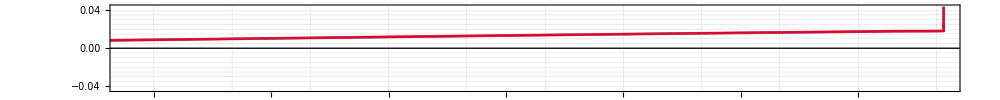
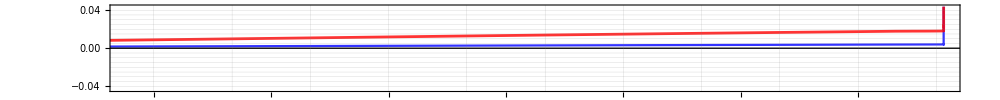
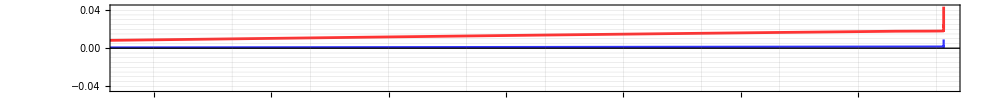
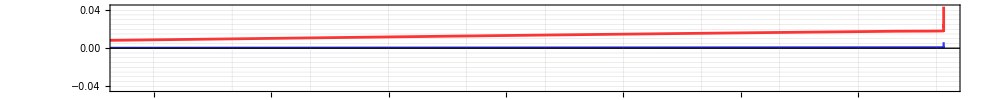
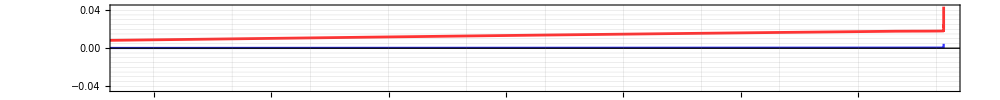
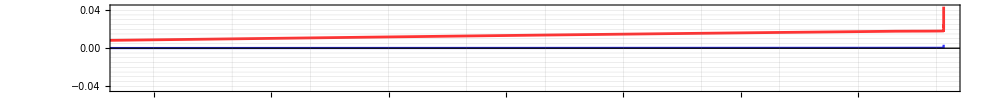
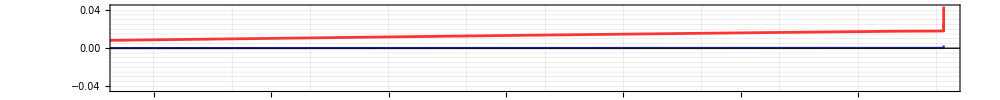
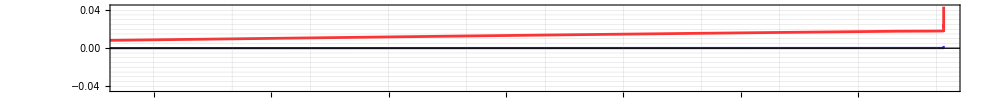
-Graphics-0.2
-Graphics-0.7
-Graphics-1.2
-Graphics-1.7
-Graphics-2.2
-Graphics-2.7
-Graphics-3.2
-Graphics-3.7
-Graphics-4.2
-Graphics-4.7
-Graphics-5.2
-Graphics-5.7
-Graphics-6.2
-Graphics-6.7
-Graphics-7.2
-Graphics-7.7
-Graphics-8.2
-Graphics-8.7
-Graphics-9.2
-Graphics-9.7
-Graphics-10.2
-Graphics-10.7
-Graphics-11.2
-Graphics-11.7

```mathematica
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

```mathematica
(*Mock-up for demonstration:Generates sample data similar to your structure*)
sampleData=ParallelTable[
Module[{data,DATA,position,w,v,fourier},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
{w,v}=Transpose[interpolateAndFourierTr[{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,{10,15}]];
Transpose[{Table[i,{j,1,Length[w]}],w,v}]
],{i,1,20,1}];

minmax=MinMax[#3&@@@Flatten[sampleData,1]];

(*Visualization code*)
Graphics3D[Table[{ColorData["BlueGreenYellow"][sampleData[[i,j,3]]/minmax[[2]]],
Cuboid[{
sampleData[[i,j,1]],
sampleData[[i,j,2]],0},
{sampleData[[i,j,1]]+0.8,sampleData[[i,j,2]]+0.095,sampleData[[i,j,3]]}]},
{i,1,Length[sampleData]},{j,1,Length[sampleData[[i]]]}],Axes->True,BoxRatios->{1,1,1/2},PlotRange->{All,{0,3},All}]
```

Set::shape: Lists {w$2359,v$2359} and {} are not the same shape.

Set::shape: Lists {w$2357,v$2357} and {} are not the same shape.

Set::shape: Lists {w$2359,v$2359} and {} are not the same shape.

Set::shape: Lists {w$2361,v$2361} and {} are not the same shape.

Set::shape: Lists {w$2359,v$2359} and {} are not the same shape.

Set::shape: Lists {w$2357,v$2357} and {} are not the same shape.

Set::shape: Lists {w$2359,v$2359} and {} are not the same shape.

Set::shape: Lists {w$2355,v$2355} and {} are not the same shape.

Set::shape: Lists {w$2357,v$2357} and {} are not the same shape.

Set::shape: Lists {w$2359,v$2359} and {} are not the same shape.

Set::shape: Lists {w$2355,v$2355} and {} are not the same shape.

Transpose::nmtx: The first two levels of {{},w$2359,v$2359} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2357,v$2357} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2359,v$2359} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2361,v$2361} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2359,v$2359} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2357,v$2357} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2359,v$2359} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2355,v$2355} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2357,v$2357} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2359,v$2359} cannot be transposed.

Transpose::nmtx: The first two levels of {{},w$2355,v$2355} cannot be transposed.

Transpose::nmtx: {{},w$2359,v$2359}の最初の2個のレベルは転置できません．

General::stop: この計算中に，Transpose::nmtxのこれ以上の出力は表示されません．

Function::slotn: #3&のスロット番号3を(#3&)[{{},w$2359,v$2359}]から満たすことができません．

General::stop: この計算中に，Function::slotnのこれ以上の出力は表示されません．

-Graphics3D-

## 収束性のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json"
jsonInfo[json]
plotstyle=Table[RGBColor[{Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i}],{i,0,1,0.2}]
rbgs=Table["#"<>StringJoin[IntegerString[Round[#],16,2]&/@({255*Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i})],{i,0,1,0.2}]
hexColor="#"<>StringJoin[IntegerString[#,16,2]&/@rbgs[[1]]]


legend={(*"0.1",*)"0.09","0.08","0.07","0.06","0.05"}
```

Available:plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
getOmegaFromKandDepth
getTFromLandDepth

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.jsonが見付かりませんでした．

no. | title | length

{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]}

{#000100,#4b0100,#7a0100,#7a0001,#4b0001,#010001}

##000100

{0.09,0.08,0.07,0.06,0.05}

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,3⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

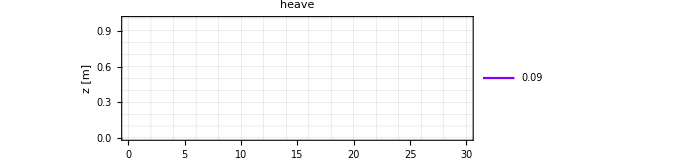

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

Part::partw: (float_COM/.$Failed)⟦1;;All,1⟧の部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

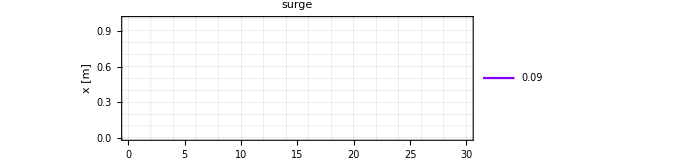

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.jsonが見付かりませんでした．

General::stop: この計算中に，Import::nffilのこれ以上の出力は表示されません．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partw: float_pitch/.$Failedの部分250は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

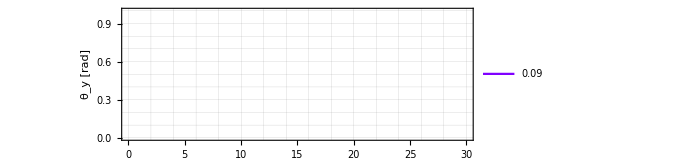

```mathematica
jsons={(*"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d1/result.json",*)
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d1/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d08/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d07/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d05/result.json"(*,
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_3/result.json"*)};

plotxrange={{0,30},All};
opt2={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
PlotStyle->plotstyle,
Joined->{True,True,True,True},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->500,
(*PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.3]},{Darker[Blue,0.6]},{Darker[Blue,0.9]}},*)
AspectRatio->1/3};
(*メッシュと計算の収束*)

fig=ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",3]-importData[jsons[[i]],"float_COM",3][[250]])}ᵀ,
{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
(*PlotRange->{{0,12.},{-0.07,0.07}},*)
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"heave",
Evaluate[plot2Doption]
]
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],(importData[jsons[[i]],"float_COM",1]-importData[jsons[[i]],"float_COM",1][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"surge",
Evaluate[plot2Doption]
]
k=2π/λ;
ListPlot[
Table[{importData[jsons[[i]],"simulation_time"],-(importData[jsons[[i]],"float_pitch"]-importData[jsons[[i]],"float_pitch"][[250]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt2],
PlotLegends->legend,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
```

```mathematica
json1="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json"
delt=0.67/(ω/k);
T=1.;
DATA1=importData[json1,"gauge0_intersection",3];
Column[ParallelTable[
Module[{data,DATA,position},
data="gauge"<>ToString[i]<>"_intersection";
DATA=importData[json,data,3];
position=importData[json,data,1][[1]];
Labeled[
ListPlot[
{{importData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
{importData[json,"simulation_time"](*+(*0.295*)delt*i*),(DATA1-DATA1[[1]])}ᵀ
(*Table[{t,-ζa*Cos[2π/T*t-k*(position)]},{t,0,30,.1}]*)
},
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
Evaluate[plot2Doption]
]
,position
,Right]
],{i,0,23,1}]
,Spacings->0
]
```

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.json

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_no_float0d09/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge1_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge2_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge3_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge4_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge5_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge9_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge11_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge13_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge14_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge15_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge17_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge20_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge23_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge7_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge8_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge10_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge1_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge2_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge3_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge4_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge5_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge6_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge9_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge11_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge12_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge13_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge14_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge15_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge16_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge17_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge18_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge19_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge20_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge21_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge23_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge7_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge8_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge10_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Part::partd: Part specification (gauge22_intersection/.$Failed)⟦1;;All,1⟧ is longer than depth of object.

Import::nffil: File /Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water0d06/result.json not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

ReplaceAll::reps: {$Failed} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification (gauge0_intersection/.$Failed)⟦1;;All,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge4_intersection/.$Failed)⟦1;;All,3⟧-(gauge4_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge5_intersection/.$Failed)⟦1;;All,3⟧-(gauge5_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge11_intersection/.$Failed)⟦1;;All,3⟧-(gauge11_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge13_intersection/.$Failed)⟦1;;All,3⟧-(gauge13_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge14_intersection/.$Failed)⟦1;;All,3⟧-(gauge14_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge16_intersection/.$Failed)⟦1;;All,3⟧-(gauge16_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge17_intersection/.$Failed)⟦1;;All,3⟧-(gauge17_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge19_intersection/.$Failed)⟦1;;All,3⟧-(gauge19_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge20_intersection/.$Failed)⟦1;;All,3⟧-(gauge20_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge23_intersection/.$Failed)⟦1;;All,3⟧-(gauge23_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge7_intersection/.$Failed)⟦1;;All,3⟧-(gauge7_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge8_intersection/.$Failed)⟦1;;All,3⟧-(gauge8_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge10_intersection/.$Failed)⟦1;;All,3⟧-(gauge10_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ListPlot::nonopt: Options expected (instead of opt) beyond position 1 in ListPlot[{{simulation_time/.$Failed,(gauge22_intersection/.$Failed)⟦1;;All,3⟧-(gauge22_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]. An option must be a rule or a list of rules.

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(gauge0_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ListPlot::nonopt: ListPlot[{{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]における1の位置より後方にオプションが想定されます（optの代りに）．オプションは規則あるいは規則のリストでなければなりません．

Part::partd: 部分指定(gauge1_intersection/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

General::stop: この計算中に，Part::partdのこれ以上の出力は表示されません．

ListPlot::nonopt: ListPlot[{{simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]における1の位置より後方にオプションが想定されます（optの代りに）．オプションは規則あるいは規則のリストでなければなりません．

ListPlot::nonopt: ListPlot[{{simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{color,color,color,color,color,color},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[color]}]における1の位置より後方にオプションが想定されます（optの代りに）．オプションは規則あるいは規則のリストでなければなりません．

ListPlot[{{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge0_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge1_intersection/.$Failed)⟦1;;All,3⟧-(gauge1_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge1_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge2_intersection/.$Failed)⟦1;;All,3⟧-(gauge2_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge2_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge3_intersection/.$Failed)⟦1;;All,3⟧-(gauge3_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge3_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge4_intersection/.$Failed)⟦1;;All,3⟧-(gauge4_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge4_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge5_intersection/.$Failed)⟦1;;All,3⟧-(gauge5_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge5_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge6_intersection/.$Failed)⟦1;;All,3⟧-(gauge6_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge6_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge7_intersection/.$Failed)⟦1;;All,3⟧-(gauge7_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge7_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge8_intersection/.$Failed)⟦1;;All,3⟧-(gauge8_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge8_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge9_intersection/.$Failed)⟦1;;All,3⟧-(gauge9_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge9_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge10_intersection/.$Failed)⟦1;;All,3⟧-(gauge10_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge10_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge11_intersection/.$Failed)⟦1;;All,3⟧-(gauge11_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge11_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge12_intersection/.$Failed)⟦1;;All,3⟧-(gauge12_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge12_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge13_intersection/.$Failed)⟦1;;All,3⟧-(gauge13_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge13_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge14_intersection/.$Failed)⟦1;;All,3⟧-(gauge14_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge14_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge15_intersection/.$Failed)⟦1;;All,3⟧-(gauge15_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge15_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge16_intersection/.$Failed)⟦1;;All,3⟧-(gauge16_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge16_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge17_intersection/.$Failed)⟦1;;All,3⟧-(gauge17_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge17_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge18_intersection/.$Failed)⟦1;;All,3⟧-(gauge18_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge18_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge19_intersection/.$Failed)⟦1;;All,3⟧-(gauge19_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge19_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge20_intersection/.$Failed)⟦1;;All,3⟧-(gauge20_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge20_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge21_intersection/.$Failed)⟦1;;All,3⟧-(gauge21_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge21_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge22_intersection/.$Failed)⟦1;;All,3⟧-(gauge22_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge22_intersection/.$Failed
ListPlot[{{simulation_time/.$Failed,(gauge23_intersection/.$Failed)⟦1;;All,3⟧-(gauge23_intersection/.$Failed)},{simulation_time/.$Failed,(gauge0_intersection/.$Failed)⟦1;;All,3⟧-(gauge0_intersection/.$Failed)}},AspectRatio→1/10,PlotRange→{Automatic,{-1.75 ζa,1.75 ζa}},Joined→{True,True,True,True,True},opt,PlotStyle→{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]},{PlotRange→Automatic,BaseStyle→Directive[FontFamily→Times New Roman,FontSize→18],PlotTheme→Scientific,Joined→True,ImageSize→400,FrameStyle→Directive[GrayLevel[0]]}]gauge23_intersection/.$Failed

## 伝播の収束のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*start=18.15;
end=30;*)
start=0;
end=30;
```

Available:plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
getOmegaFromKandDepth
getTFromLandDepth

```mathematica
importData[filename_String,var_,n_: 0,replacement_: Missing[]]:=Module[{imported=Import[filename],processed},processed=imported/.{"NaN"|"Nan"|"null"|"nan"|Null->replacement};
If[n>0,(var/.processed)[[;;,n]],var/.processed]];

fileDir="/Volumes/home/BEM/benchmark20250220";
(*fileDir="/Users/tomoaki/BEM";*)
```

```mathematica
/Volumes/home/BEM/benchmark20250220/Tanizawa1996_H0d05_T1d0_DT0d1_MESHwater_no_float0d08_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_no_float
```

```mathematica
jsons={
"Tanizawa1996_H0d05_T1d0_DT0d1_MESHwater_no_float0d08_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_no_float","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALElinear",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad"};
jsons=FileNameJoin[{fileDir,#,"result.json"}]&/@jsons;
```

```mathematica
ExtractInfoFromPath[path_String]:=Module[{splitPath,mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod},splitPath=StringSplit[path,{"_","/"}];
(*Hの値を抽出*)
h=SelectFirst[splitPath,StringContainsQ[#,"H0d"]&];
h=StringReplace[h,{"H0d"->"H=0."}];

(*dtの値を抽出*)
dt=SelectFirst[splitPath,StringContainsQ[#,"DT0d"]&];
dt=StringReplace[dt,{"DT0d"->"dt=0."}];

(*meshの値を抽出*)
mesh=SelectFirst[splitPath,StringContainsQ[#,"float0d"]&];
mesh=StringReplace[mesh,{"float0d"->"dl=0."}];

(*BVPとIVPのための要素を抽出*)
elementBVPandIVP=SelectFirst[splitPath,StringContainsQ[#,"ELEM"]&];
elementBVPandIVP=StringReplace[elementBVPandIVP,"ELEM"->"BVP:"];

(*ALEの要素を抽出*)
elementALE=SelectFirst[splitPath,StringContainsQ[#,"ALE"]&];
elementALE=StringReplace[elementALE,"ALE"->"ALE:"];

(*ALE periodの値を抽出*)
ALEperiod=SelectFirst[splitPath,StringContainsQ[#,"ALEPERIOD"]&,"ALEPERIOD1"];
ALEperiod=StringReplace[ALEperiod,{"ALEPERIOD"->"ALE Step Period:"}];


(*結果を返す*)
{mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod}];

(*gauges={"gauge2_intersection","gauge22_intersection"};*)
(*gauges={"gauge4_intersection","gauge23_intersection"};*)
gauges={"gauge2_intersection","gauge22_intersection"};
colors={Blue,Red,Darker[Green],Black};
(*---------------------------------------------*)
compare[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)



legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];
(*=======================================================================*)
Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.925,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,gauges}]]
,framelabel["Time [s]","Surface Elevation [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
},
{
Labeled[
Row[Table[ListStepPlot[Table[{#1,#2}&@@@(interpolateAndFourier[#1,#2]&@@Transpose[selectAndNegateMean[json,name]]),{json,jsons}]
,Center
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio*2.
,ImageSize->size/2.
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.85,0.85}]]
,PlotRange->{{0.,3},{All,zrange[[2]]}(*,{0,0.026}*)}
,Joined->False
,Filling->Bottom
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]
],
{name,gauges}]]
,framelabel["Frequency [s^-1]","Amplitude.08 [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
]
]
(*=======================================================================*)
compareSimple[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)

legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];

Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio/1.5
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.05,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,{
"gauge2_intersection",
"gauge7_intersection",
"gauge12_intersection",
"gauge17_intersection",
"gauge22_intersection"}}]]
,framelabel["Time [s]","Surface Elevation [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
,Spacings->0]
]
(*=======================================================================*)
fileName[{H_,L_,WAVE_,MESH_,DT_,ELEM_,ALE_}]:=Module[{formatNumber},
formatNumber[n_]:=StringReplace[ToString[N[n]],"."->"d"];
StringJoin["Tanizawa1996_",
"H",formatNumber[H],
"_L",formatNumber[L],
"_WAVE",WAVE,
"_MESH",MESH,
"_DT",formatNumber[DT],
"_ELEM",ELEM,
"_ALE",ALE]]
```

```mathematica
(*gaugeのx座標*)
FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[2]],1][[1]]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[1]],1][[1]]
```

/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.json

Import::nffil: Importの最中にファイル/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge22_intersection/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

gauge22_intersection/.$Failed

Import::nffil: Importの最中にファイル/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge2_intersection/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

gauge2_intersection/.$Failed

```mathematica
(*少しチェック*)
F=getOmegaFromLandDepth[1.8,50.]/(2*π)
T=1/F
```

0.93134

1.07372

```mathematica
2*π/getOmegaFromLandDepth[1.8,5.]
```

1.07372

#### 減衰へのALE毎回．meshの細かさの影響（おいおい）

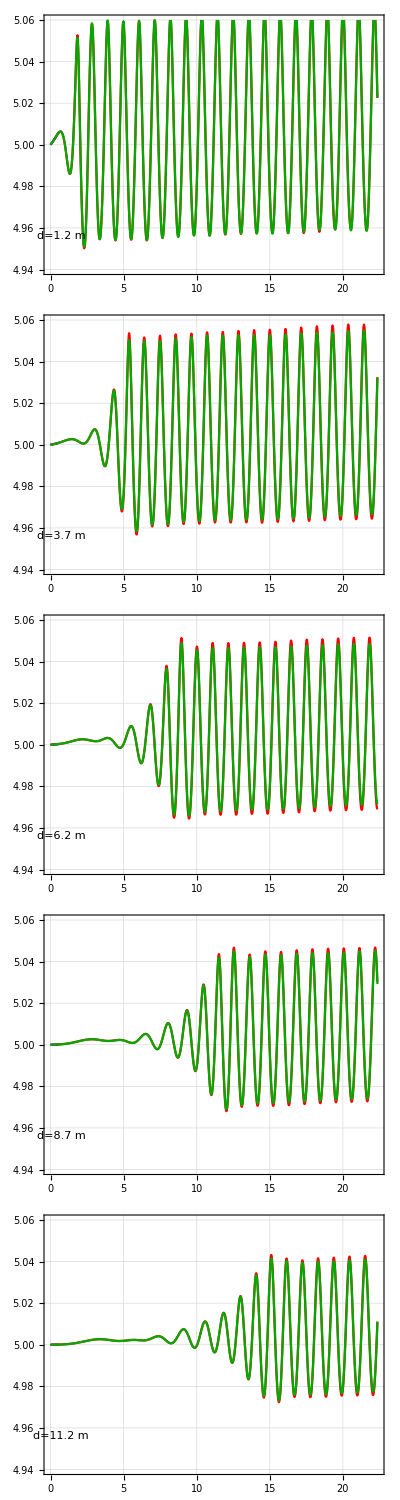
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png

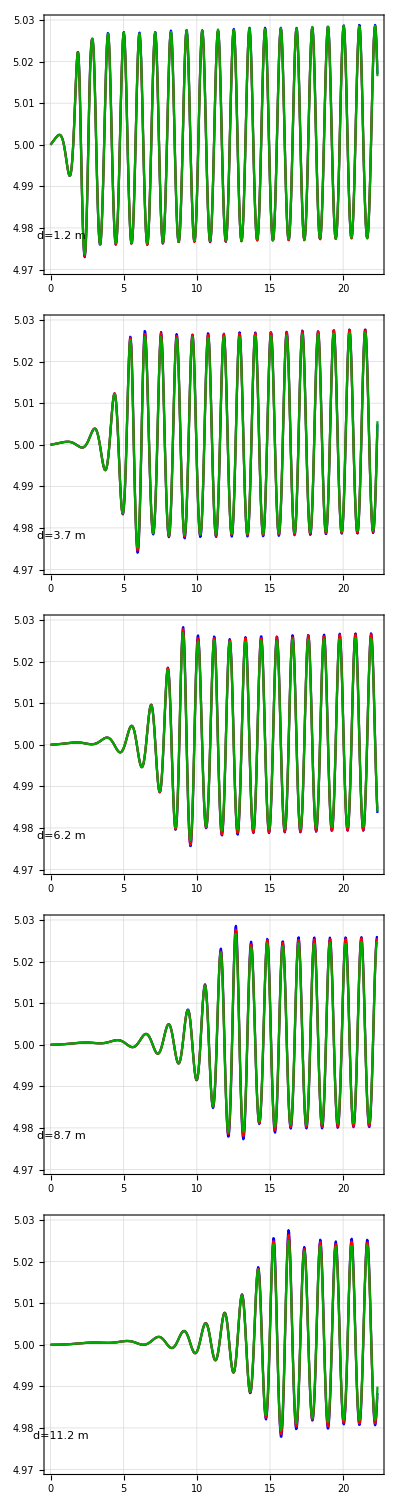
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.06,0.06};
{start,end}={0.,17.+T*5};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d05_T1d0_DT0d1_MESHwater_no_float0d08_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_no_float"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_T1d0_DT0d1_MESHwater_no_float0d08_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};
fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]
Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png",fig,ImageResolution->300]

comp0d08={
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};

fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,{-0.03,0.03}]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png",fig,ImageResolution->300]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:linear

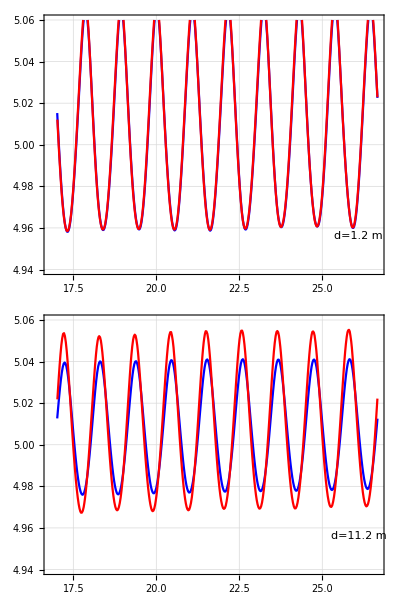
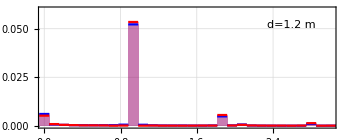
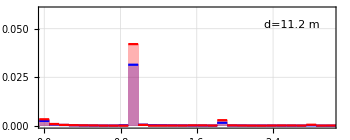
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_comparison.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={17.,17.+T*9};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};

fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_comparison.png",fig,ImageResolution->225]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:pseudo-quad

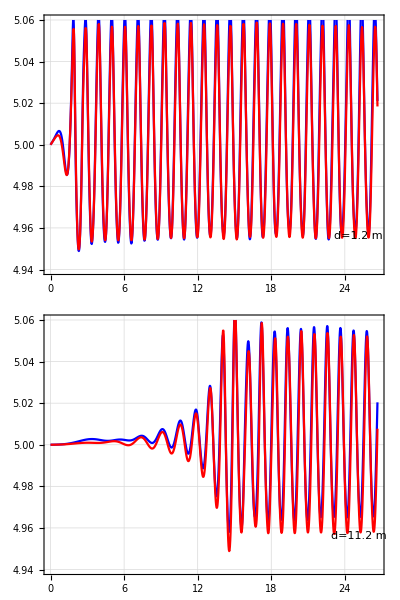
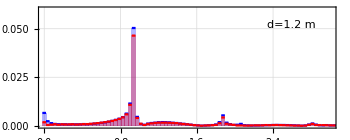
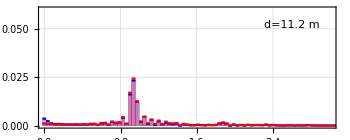
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png

ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={0.,17.+T*9};
ALE="pseudo_quad";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};*)

comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};


fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png",fig,ImageResolution->225]

Text["ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．"]
```

#### BVPに擬2次要素を使った場合

{Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1,Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1}

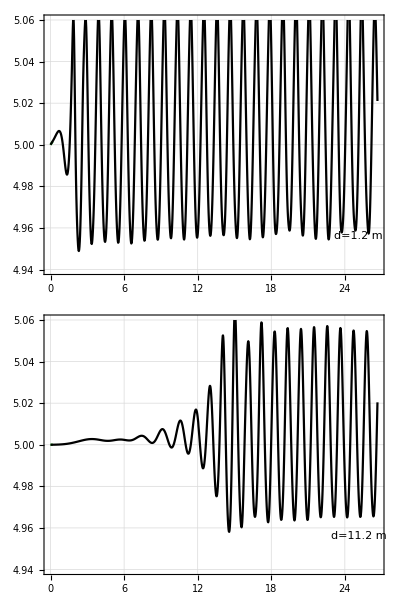
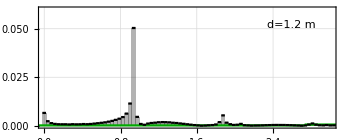
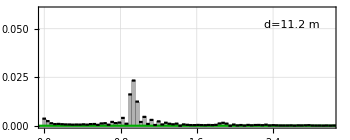
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/MESH0d08_ELEMpseudo_quad_H0d1.png

ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．

```mathematica
zrange={-0.03,0.03}*2.;
colors=RotateLeft[colors,2];
ALE="pseudo_quad";
BVP="linear";
comp={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"}

compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/MESH0d08_ELEMpseudo_quad_H0d1.png",%,ImageResolution->225]

Text["ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．"]
```

#### 最も良いと思われる計算

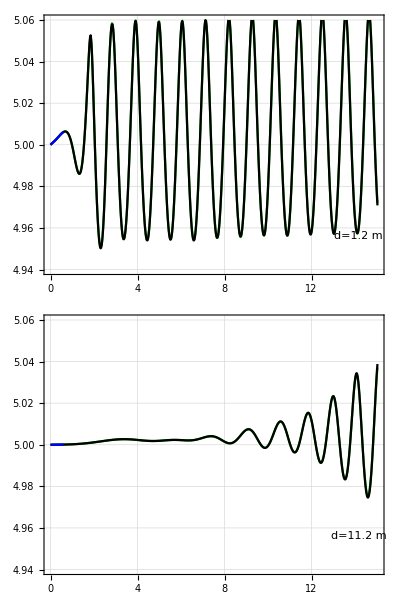
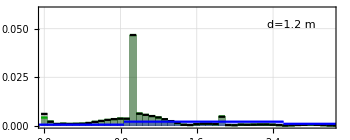
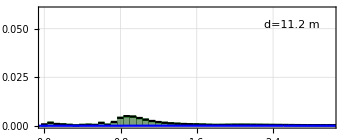
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={0.,T*14};
ALE="pseudo_quad";
fileDir="/Volumes/home/BEM/benchmark202405";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};*)

comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1"};


fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

(*Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png",fig,ImageResolution->225]
*)
Text["ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．"]
```

{141.12,152.64,190.08,204.48}

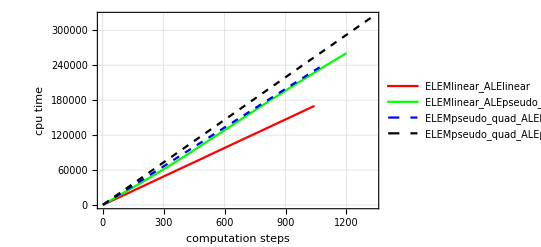

{141.12,152.64,190.08,204.48}

{1.,1.08163,1.34694,1.44898}

```mathematica
list={
"ELEMlinear_ALElinear",
"ELEMlinear_ALEpseudo_quad",
"ELEMpseudo_quad_ALElinear",
"ELEMpseudo_quad_ALEpseudo_quad"};
(*clist={5000,6000,7000,8000}*0.96;*)
clist={4900,5300,6600,7100}*0.96*0.03
Show[ListPlot[
Table[importData["/Volumes/home/BEM/benchmark202404/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_"<>name<>"/result.json","cpu_time"]
(*}*)
,{name,list}]
,FrameLabel->framelabel["computation steps","cpu time"]
,PlotStyle->{Red,{Green},{Blue,Dashed},{Black,Dashed}}
,PlotLegends->list
,GridLines->Automatic
(*,PlotRange->{{0,10},Automatic}*)
,Evaluate[plot2Doption]]
(*,
Plot[Table[c*x,{c,clist}],{x,0,10}]*)
]

clist
clist/clist[[1]]
```